# Visualizing Sequence Alignments from the 2019-nCov

## By: Jessica Shi

I created a DNA sequence alignment visual tool while I was at the Wolfram Summer Camp 2019. These tools can be used to quickly analyze many sequences in reference to one sequence. Organisms that share similar bases and have similar sequence lengths and high alignment scores are more likely to have similar structure and function for that particular gene. It provides a large variety of visuals including charts and figures to compare the sequences for different purposes. It takes into account short sequence/long sequence differentiation and other syntactical differences. I used this tool that I created to analyze the new data in the Data Repository for the Wuhan novel coronavirus. How I created this sequence visualizer is detailed in a post I made in the summer. 

I enjoyed hosting a livestream with Rory Foulger on Friday, as we explored the various datasets that were recently added to the Wolfram database. These are some of the examples I played around with my visualizer function.

## Analyzing Genomes from Different Countries

Pull the data from the data repository

```mathematica
geneticdata=ResourceData["Genetic Sequences of 2019-2020 Wuhan Coronavirus Outbreak"]
```

Dataset[<>]

First, I chose to compare 2 sequences from China, 1 sequence from the United States, and 1 sequence from Australia with the reference sequence.

Extract the sequences from data

```mathematica
china1=Normal[geneticdata][[8]]["Sequence"];
china2=Normal[geneticdata][[25]]["Sequence"];
australia=Normal[geneticdata][[5]]["Sequence"];
unitedstates=Normal[geneticdata][[15]]["Sequence"];
refseq=Normal[geneticdata][[36]]["Sequence"];
```

Since these genomes are going to be practically identical, an important factor is also when this virus was collected and sampled to see how much the virus mutated over time.

```mathematica
Grid[{{"Reference Sequence","China",Normal[geneticdata][[36]]["CollectionDate" ]},
{"Sequence 1","China",Normal[geneticdata][[8]]["CollectionDate" ]},
{"Sequence 2","China",Normal[geneticdata][[25]]["CollectionDate" ]},
{"Sequence 3", "Australia",Normal[geneticdata][[5]]["CollectionDate" ]},
{"Sequence 4","United States",Normal[geneticdata][[15]]["CollectionDate" ]}},Frame->All]
```

Reference Sequence | China | Month: Dec 2019
Sequence 1 | China | Day: Mon 30 Dec 2019
Sequence 2 | China | Month: Jan 2020
Sequence 3 | Australia | Day: Sat 25 Jan 2020
Sequence 4 | United States | Day: Wed 22 Jan 2020

Perform alignment and create visuals

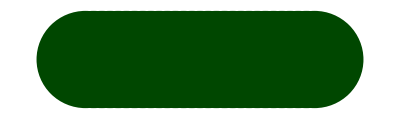
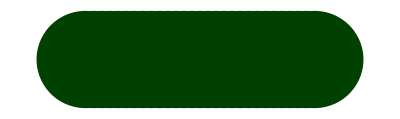
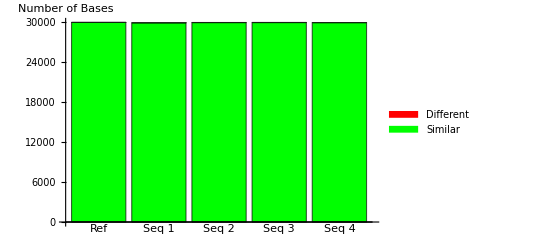
name | first 30 bases | length of sequence |  |  |  |  | 
Reference | ATTAAAGGTTTATACCTTCCCAGGTAACAA | 29903 |  |  |  |  | 
Sequence 1 | CCTTCCCAGGTAACAAACCAACCAACTTTC | 29854 | 29854 | 29854. | 29805. | 29854 | 100%
Sequence 2 | ATTAAAGGTTTATACCTTCCCAGGTAACAA | 29891 | 12536 | 29881. | 29869. | 29886 | 99.98%
Sequence 3 | ATTAAAGGTTTATACCTTCCCAGGTAACAA | 29893 | 19064 | 29877. | 29877. | 29890 | 99.99%
Sequence 4 | ATTAAAGGTTTATACCTTCCCAGGTAACAA | 29882 | 17060 | 29874. | 29853. | 29878 | 99.99%
name |  |  |  | 
Sequence 1 | -Graphics- |  |  | 
Sequence 2 | -Graphics- |  |  | 
Sequence 3 | -Graphics- |  |  | 
Sequence 4 | -Graphics- |  |  | 

-Graphics-12

```mathematica
tables[{refseq,{china1,china2,australia,unitedstates}}]
```

As you can see, these sequences are practically perfectly identical, as expected. It is interesting to note that the genomes collected later in January (2-4) had more differences with the reference sequence that was first collected in December than the genome collected on December 30 (Sequence 1).

## Comparing 2019-nCov with SARS and MERS

I also wanted to see how the 2019 - nCov would compare to the SARS virus of 2003 and the MERS virus of 2012. I used the NCBI Gene Bank and the "Import FASTA" function from the repository to get the genetic data for those two viruses.

Import sequence data for SARS and MERS

```mathematica
sars=First@ResourceFunction["ImportFASTA"]["NC_004718.3"][[2]];
```

```mathematica
mers=First@ResourceFunction["ImportFASTA"]["NC_019843.3"][[2]];
```

This is the result for the comparison:

Perform alignment and create visuals

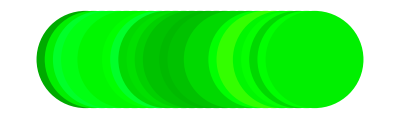
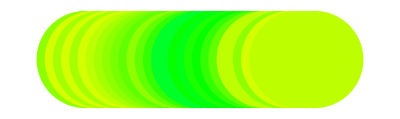
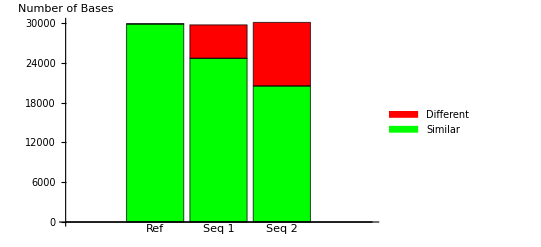
name | first 30 bases | length of sequence |  |  |  |  | 
Reference | ATTAAAGGTTTATACCTTCCCAGGTAACAA | 29903 |  |  |  |  | 
Sequence 1 | ATATTAGGTTTTTACCTACCCAGGAAAAGC | 29751 | AATGCTAGGGAGAGCTGCCTATATGGAAGAGCCCTAATGTGTAAAATTAATTTTAGTAGTGCTATCCCCATGTGATTTTAATAGCTTCTTAGGAGAATGACAAAAAAAAAAAAAAAAAAAAAAAA | 18700. | 18690. | 24700 | 83.02%
Sequence 2 | GATTTAAGTGAATAGCTTGGCTATCTCACT | 30119 | TTTAAATATTGGGATCAGAC | 7493. | 7471. | 20525 | 68.15%
name |  |  |  | 
Sequence 1 | -Graphics- |  |  | 
Sequence 2 | -Graphics- |  |  | 

-Graphics-12

```mathematica
tables[{refseq,{sars,mers}}]
```

The SARS virus is a lot more similar to the 2019-nCov than the MERS virus. Even though they do have a high level of alignment, as scientists have determined, there is enough genetic difference to label the Wuhan virus as a “novel coronavirus” .